# 1. NALOGA

```mathematica
trikotnik={{0, 0}, {5, 1}, {7, 4}}
```

{{0,0},{5,1},{7,4}}

```mathematica
Stranice[{AA_, BB_, CC_}]:= {{BB, CC}, {CC, AA}, {AA, BB}}
Stranice[trikotnik]
```

{{{5,1},{7,4}},{{7,4},{0,0}},{{0,0},{5,1}}}

```mathematica
stranice1= Map[Line,{{AA, BB}, {BB, CC}, {AA, CC}}]
```

{Line[{{0,0},{5,1}}],Line[{{5,1},{7,4}}],Line[{{0,0},{7,4}}]}

```mathematica
Koti[{AA_, BB_, CC_}]:= {{CC, AA, BB}, {AA, BB, CC}, {BB, CC, AA}}
Koti[trikotnik]
```

{{{7,4},{0,0},{5,1}},{{0,0},{5,1},{7,4}},{{5,1},{7,4},{0,0}}}

```mathematica
AA:={0, 0}
BB:={5, 1}
CC:={7, 4}
SlikaOgljisc[trikotnik_]:= {AA, BB, CC}
stranice = Map[Point, trikotnik]
```

{Point[{0,0}],Point[{5,1}],Point[{7,4}]}

```mathematica
Graphics[{ PointSize[Large],stranice}]
```

-Graphics-

```mathematica
SlikaStranic[trikotnik_]:= {{AA, BB}, {BB, CC}, {AA, CC}}
stranice1
```

{Line[{{0,0},{5,1}}],Line[{{5,1},{7,4}}],Line[{{0,0},{7,4}}]}

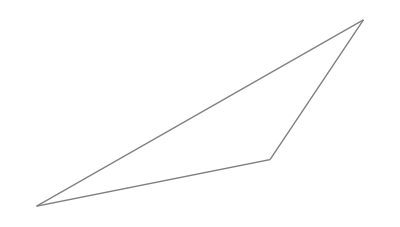

```mathematica
Graphics[{Gray,stranice1}]
```

```mathematica
NarisiTrikotnik[trikotnik_]:= {{stranice1, trikotnik}}
```

```mathematica
NarisiTrikotnik[trikotnik_]:=Graphics[{ PointSize[0.05], RGBColor[1,0,0],Thickness[Large], stranice, stranice1}]
```

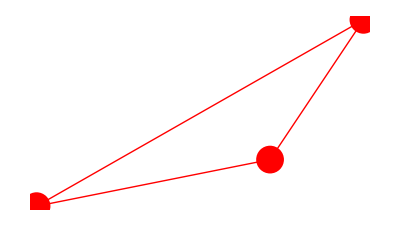

```mathematica
NarisiTrikotnik[trikotnik]
```

```mathematica
2.NALOGA
```

```mathematica
VektorSimetraleKota[{x_, y_, z_}]:= Normalize[Normalize[x-y]+Normalize[z-y]]
```

```mathematica
VektorSimetraleKota[Koti[trikotnik][[1]]]//N
```

{0.936505,0.350655}

```mathematica
VektorSimetraleKota[Koti[trikotnik][[2]]]//N
```

{-0.55644,0.830888}

```mathematica
VektorSimetraleKota[Koti[trikotnik][[3]]]//N
```

{-0.731027,-0.682348}

```mathematica
ClearAll[SimetralaKota]
```

```mathematica
SimetralaKota[{x_, y_, z_}, dol_:10]:= {y, y + VektorSimetraleKota[{x, y, z}] * dol}
SimetralaKota[Koti[trikotnik][[1]],100]//N
```

{{0.,0.},{93.6505,35.0655}}

```mathematica
3.NALOGA
```

```mathematica
SlikaSimetralKotov[trikotnik_, dol:10]:=
```

```mathematica
SlikaStranic[{[trikotnik], Line[SimetralaKota[Koti[trikotnik][[1]]]]}]
```

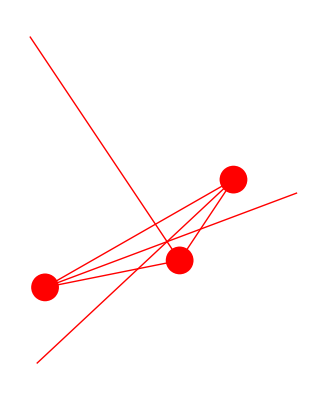

```mathematica
Graphics[{PointSize[0.05], RGBColor[1,0,0],Thickness[Large], stranice, stranice1, Map[Line, Map[SimetralaKota, Koti[trikotnik]]]}]//N
```